# Independent Fourier-Galerkin Validation

Mathematica 9 launcher for the frozen dual-mode conformal-metasurface configurations. This notebook loads a self-contained spectral package. It does not load or call DualModeRIS.m.

## 1. Load the independent package

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\mrkho_000\Desktop\IEEE_TAP_DualMode_Metasurface\FourierGalerkin_Mathematica9_Validation

```mathematica
Get["FourierGalerkinValidation.m"]
```

## 2. Run the mandatory checks

```mathematica
fgSelfTestResult=FGSelfTest[]
```

FGSelfTest: starting independent Fourier--Galerkin checks...

check | measured value | criterion | status
frozen input dimensions and passivity | 0.03 | minimum Re[Z] >= 0 and correct lengths | PASS
piecewise Fourier coefficients | 1.589×10^-6 | relative error <= 2*10^-5 | PASS
admittance multiplication matrix orientation | 1.44921×10^-6 | relative error <= 3*10^-5 | PASS
constant-impedance closed-form solution | 1.80249×10^-16 | relative error <= 10^-11 | PASS
modal field versus direct boundary quadrature | 2.49434×10^-13 | relative error <= 10^-6 | PASS
frozen low-scattering projected residual | 2.06734×10^-15 | relative residual <= 10^-11 | PASS
frozen telemetry projected residual | 2.41208×10^-15 | relative residual <= 10^-11 | PASS
all reported test values finite | 1 | value = 1 | PASS

FGSelfTest PASSED.

{Passed→True,Checks→{{frozen input dimensions and passivity,0.03,minimum Re[Z] >= 0 and correct lengths,PASS},{piecewise Fourier coefficients,1.589×10^-6,relative error <= 2*10^-5,PASS},{admittance multiplication matrix orientation,1.44921×10^-6,relative error <= 3*10^-5,PASS},{constant-impedance closed-form solution,1.80249×10^-16,relative error <= 10^-11,PASS},{modal field versus direct boundary quadrature,2.49434×10^-13,relative error <= 10^-6,PASS},{frozen low-scattering projected residual,2.06734×10^-15,relative residual <= 10^-11,PASS},{frozen telemetry projected residual,2.41208×10^-15,relative residual <= 10^-11,PASS},{all reported test values finite,1,value = 1,PASS}}}

The production study starts only if every self-test passes. The default retained half-orders are M = 64, 128, 192, and 256, corresponding to 129, 257, 385, and 513 complex Fourier modes.

## 3. Run the independent validation

FGRunValidation: the original DualModeRIS.m package is not loaded.

FGRunValidation: retained half-orders M = {64,128,192,256}.

Solving M = 64 (129 complex Fourier modes)...

worst sector = -8.256 dB; telemetry D_2D = 13.068 dB; wall time = 7.74 s.

Solving M = 128 (257 complex Fourier modes)...

worst sector = -11.197 dB; telemetry D_2D = 13.028 dB; wall time = 12.39 s.

Solving M = 192 (385 complex Fourier modes)...

worst sector = -11.320 dB; telemetry D_2D = 13.020 dB; wall time = 20.05 s.

Solving M = 256 (513 complex Fourier modes)...

worst sector = -11.358 dB; telemetry D_2D = 13.018 dB; wall time = 43.54 s.

FGRunValidation: numerical acceptance checks

check | measured | tolerance | unit | status
final-two-order worst-sector change | 0.0383005 | 0.5 | dB | PASS
final-two-order mean-sector change | 0.0482809 | 0.5 | dB | PASS
final-two-order telemetry directivity change | 0.00261942 | 0.2 | dB | PASS
final-two-order telemetry sidelobe change | 0.0313903 | 0.5 | dB | PASS
final-two-order beam-angle change | 0. | 0.5 | deg | PASS
final-two-order main-sector-efficiency change | 0.000359761 | 0.01 | absolute | PASS
maximum final low-scattering projected residual | 3.21785×10^-15 | 1/10000000000 | relative | PASS
final telemetry projected residual | 5.56445×10^-15 | 1/10000000000 | relative | PASS

FGRunValidation: cross-solver comparison

metric | unit | MoM 256 | MoM 384 | FG final | FG-MoM256 | tolerance | status
worst protected-sector power ratio | dB | -11.5751 | -11.3848 | -11.3582 | 0.216937 | 1. | PASS
mean protected-sector power ratio | dB | -13.0885 | -12.8788 | -13.1113 | -0.0227312 | 1. | PASS
telemetry main-sector efficiency | absolute | 0.649055 | 0.643549 | 0.625791 | -0.0232632 | 0.04 | PASS
telemetry two-dimensional directivity | dB | 13.0985 | 13.0819 | 13.0176 | -0.0808214 | 0.25 | PASS
telemetry peak sidelobe level | dB | -13.6013 | -13.4722 | -13.0775 | 0.523725 | 0.75 | PASS
telemetry beam angle | deg | 1. | 1.5 | 2. | 1. | 1. | PASS

FGRunValidation: results written to C:\Users\mrkho_000\Desktop\IEEE_TAP_DualMode_Metasurface\FourierGalerkin_Mathematica9_Validation\fourier_galerkin_results

-Graphics-

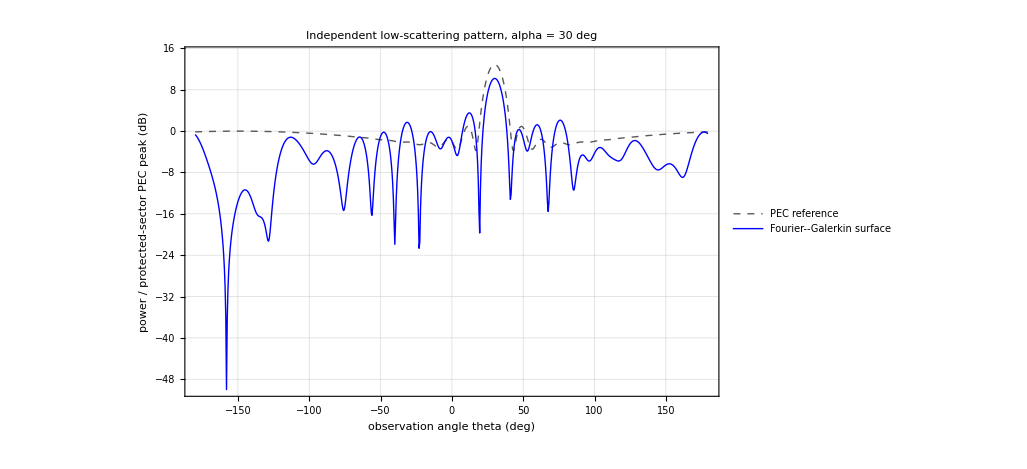

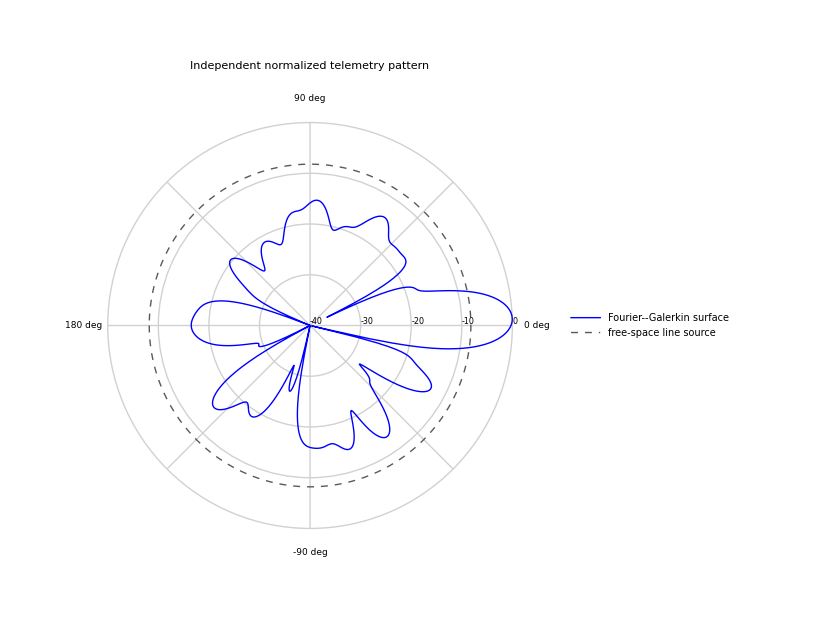

{PassedNumericalChecks→True,«4»,CrossSolverComparison→{{worst protected-sector power ratio,dB,-11.5751,-11.3848,-11.3582,0.216937,1.,PASS},{mean protected-sector power ratio,dB,-13.0885,-12.8788,-13.1113,-0.0227312,1.,PASS},«3»,{telemetry beam angle,deg,1.,1.5,2.,1.,1.,PASS}}}

```mathematica
fgStudySummary=If[TrueQ["Passed"/.fgSelfTestResult],FGRunValidation[FGRunSelfTest->False],Print["Production run cancelled because FGSelfTest did not pass."]]
```

The results are written to the fourier_galerkin_results folder beside this notebook. Review fg_validation_summary.txt first, followed by the convergence, acceptance-check, and cross-solver CSV files.